```mathematica
sample0p811 = {{0.041, 27/289}, {0.086, 45/289}, {0.15, 59/289}, {0.30, 89/289}, {0.71, 135/289}, {1.46, 193/289}, {2.77, 289/289}};
```

```mathematica
sample0p794 = {{0.041, 9/86}, {0.086, 12/86}, {0.15, 19/86}, {0.30, 26/86}, {0.71, 42/86}, {1.46, 56/86}, {2.77, 86/86}};
```

```mathematica
sample45p811 = {{0.041, 34/348}, {0.086, 52/348}, {0.15, 72/348}, {0.30, 103/348}, {0.71, 161/348}, {1.46, 234/348}, {2.77, 348/348}};
```

```mathematica
sample45p794 = {{0.041, 7/68}, {0.086, 10/68}, {0.15, 15/68}, {0.30, 21/68}, {0.71, 32/68}, {1.46, 45/68}, {2.77, 68/68}};
```

```mathematica
sampleM45p811 = {{0.041, 37/367}, {0.086, 53/367}, {0.15, 81/367}, {0.30, 116/367}, {0.71, 175/367}, {1.46, 255/367}, {2.77, 367/367}};
```

```mathematica
sampleM45p794 = {{0.041, 8/79}, {0.086, 10/79}, {0.15, 16/79}, {0.30, 25/79}, {0.71, 36/79}, {1.46, 54/79}, {2.77, 79/79}};
```

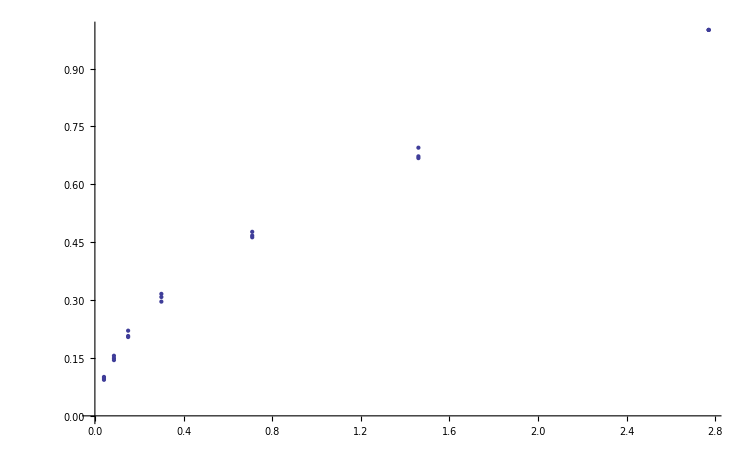

```mathematica
Show[ListPlot[sample0p811], ListPlot[sample45p811], ListPlot[sampleM45p811]]
```

```mathematica
F[a_, b_, x_] := a*Log[1+b*x];
```

```mathematica
Manipulate[Show[ListPlot[sample0p811], ListPlot[sample45p811], ListPlot[sampleM45p811], Plot[F[a, b, x], {x, 0, 4}]], {a, 0.1, 2.0}, {b, 0.05, 10.0}]
```

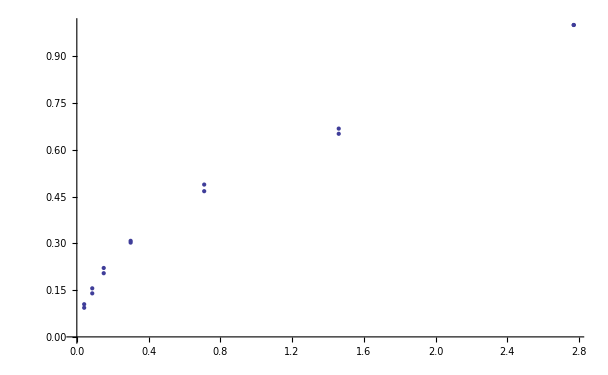

```mathematica
Show[ListPlot[sample0p811], ListPlot[sample0p794]]
```

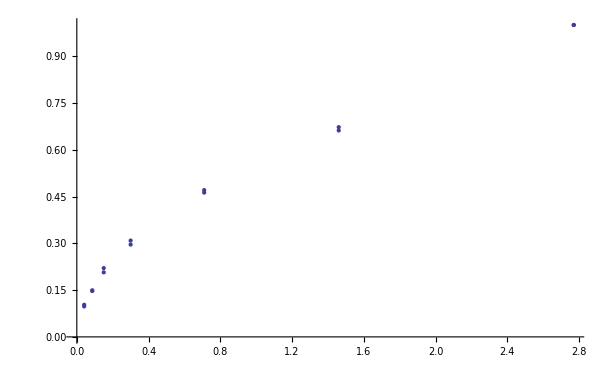

```mathematica
Show[ListPlot[sample45p811], ListPlot[sample45p794]]
```

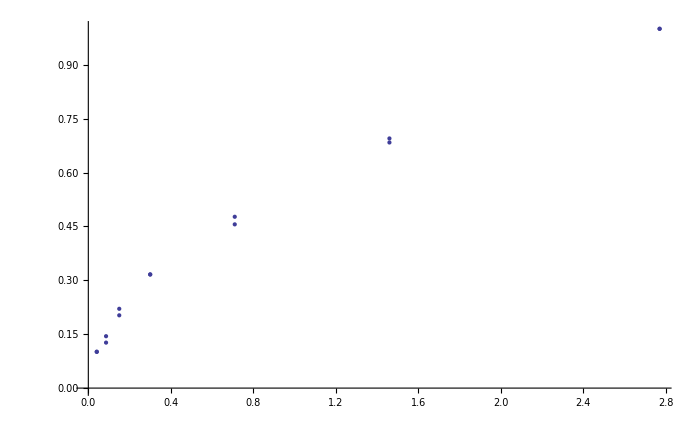

```mathematica
Show[ListPlot[sampleM45p811], ListPlot[sampleM45p794]]
```

```mathematica
FindFit[sample0p811, F[a, b, x], {a, b}, x]
```

{a→0.388969,b→3.77764}

```mathematica
FindFit[sample0p794, F[a, b, x], {a, b}, x]
```

{a→0.374669,b→4.10285}

```mathematica
FindFit[sample45p811, F[a, b, x], {a, b}, x]
```

{a→0.401182,b→3.51858}

```mathematica
FindFit[sample45p794, F[a, b, x], {a, b}, x]
```

{a→0.376839,b→4.05603}

```mathematica
FindFit[sampleM45p811, F[a, b, x], {a, b}, x]
```

{a→0.376123,b→4.22271}

```mathematica
FindFit[sampleM45p794, F[a, b, x], {a, b}, x]
```

{a→0.403355,b→3.509}

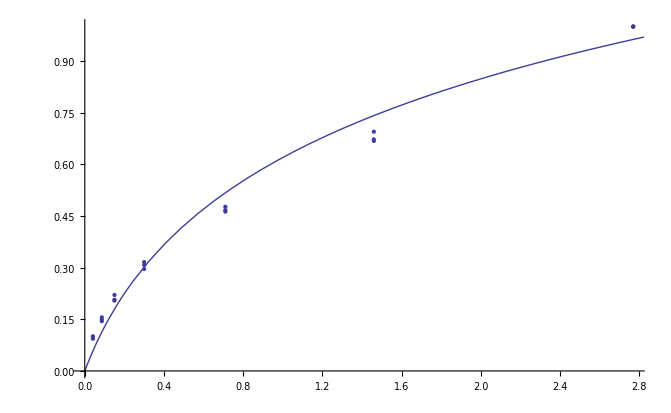

```mathematica
Show[ListPlot[sample0p811], ListPlot[sample45p811], ListPlot[sampleM45p811], Plot[F[a, b, x]/.{a->0.39, b->3.9}, {x, 0, 4}]]
```

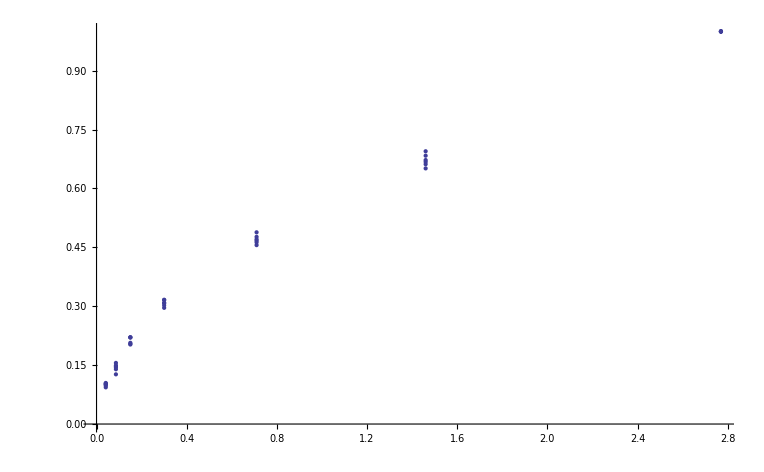

```mathematica
Show[ListPlot[sample0p811], ListPlot[sample0p794], ListPlot[sample45p811],  ListPlot[sample45p794], ListPlot[sampleM45p811], ListPlot[sampleM45p794] ]
```

```mathematica
S[p_] := 0.39*Log[1+3.9*p];
```

```mathematica
Iperp[P_, x_] := S[P*Cos[Pi/4+x]^2]*Cos[Pi/4-x]^2 + S[P*Cos[Pi/4-x]^2]*Cos[Pi/4-x]^2;
```

```mathematica
Iparall[P_, x_] := S[0.46*P*Cos[Pi/4+x]^2]*Cos[Pi/4+x]^2 + S[0.46*P*Cos[Pi/4-x]^2]*Cos[Pi/4-x]^2;
```

```mathematica
polariz[alpha_] := (Iparall[2.99, alpha] - Iperp[2.99, alpha])/(Iparall[2.99, alpha] + Iperp[2.99, alpha]);
```

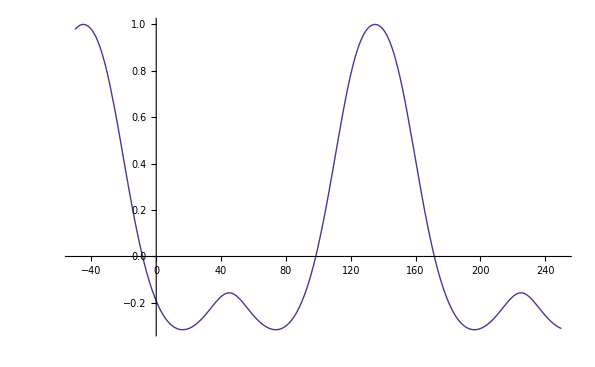

```mathematica
Plot[polariz[Pi*alpha/180], {alpha, -50, 250}]
```

```mathematica
sample0 = {{0.041, 27/289},{0.05, 33/289}, {0.086, 45/289},{0.12, 48/289}, {0.15, 59/289},{0.24, 67/289}, {0.30, 89/289}, {0.49, 95/289}, {0.71, 135/289},{1.00, 147/289} ,{1.46, 193/289},{1.82, 195/289}, {2.77, 289/289}, {3.92, 308/289}};
```

```mathematica
FindFit[sample0, F[a, b, x], {a, b}, x]
```

{a→0.403248,b→3.11988}

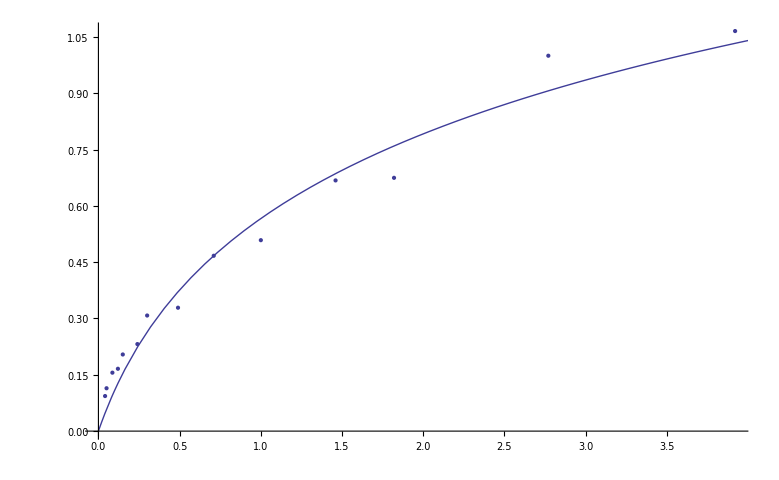

```mathematica
Show[ListPlot[sample0], Plot[F[a, b, x]/.{a->0.40, b->3.12}, {x, 0, 4}]]
```

```mathematica
Sat[p_] := 0.40*Log[1+3.12*p]
```

```mathematica
Sat[3.2]/Sat[1.5]
```

1.37968

```mathematica
S = { {0.041, 27}, {0.086, 45}, {0.15, 59}, {0.30, 89}, {0.71, 135}, {1.46, 193}, {2.77, 289} };
```

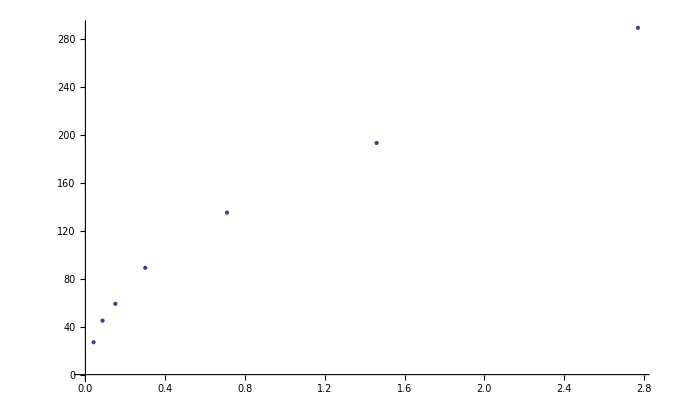

```mathematica
ListPlot[S]
```

```mathematica
FindFit[S, F[a, b, x], {a, b}, x]
```

FindFit::nrlnum: The function value {-93.6872 + 0.\ ⅈ, -74.9768 + 156.464\ ⅈ, -32.5843 + 156.464\ ⅈ, -15.2193 + 156.464\ ⅈ, -12.1714 + 156.464\ ⅈ, -32.1403 + 156.464\ ⅈ, -95.3221 + 156.464\ ⅈ} is not a list of real numbers with dimensions {7} at {a, b} = {49.8039, -17.9973}.

{a→49.8039,b→-17.9973}

```mathematica
Manipulate[Show[ListPlot[S], Plot[F[a, b, x], {x, 0, 4}]], {a, 10, 200}, {b, 0.05, 10.0}]
```